```mathematica
probdens[x_,t_,d_]:=1/(2 d^2)π^2 ((FresnelC[(d-x)/(√π √t)]+FresnelC[(d+x)/(√π √t)])^2+(FresnelS[(d-x)/(√π √t)]+FresnelS[(d+x)/(√π √t)])^2)
```

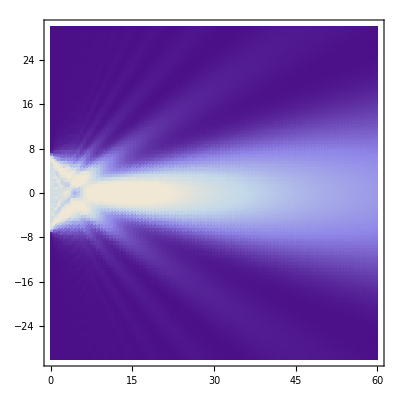

```mathematica
DensityPlot[probdens[y,x,7],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->26},AspectRatio->1]
```

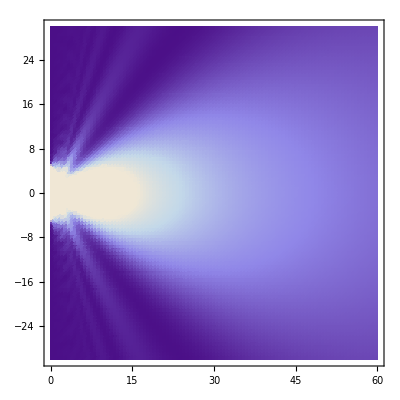

```mathematica
VelocityField3[x_, t_, d_ ]:=-(√(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
VelocityField6[x_, t_, d_ ]:=(2 Sin[(d x)/t] (Cos[(d^2+x^2)/(2 t)] (FresnelC[(d-x)/(√π √t)]+FresnelC[(d+x)/(√π √t)])+(FresnelS[(d-x)/(√π √t)]+FresnelS[(d+x)/(√π √t)]) Sin[(d^2+x^2)/(2 t)]))/(√π √t ((FresnelC[(d-x)/(√π √t)]+FresnelC[(d+x)/(√π √t)])^2+(FresnelS[(d-x)/(√π √t)]+FresnelS[(d+x)/(√π √t)])^2))
```

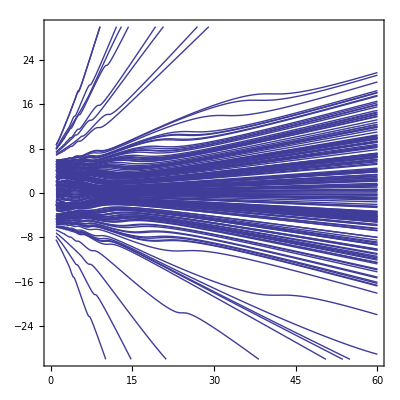

```mathematica
ddd = 7.0;
www=1.0;
kkk = 1.0;
Parallelize[
HollandtablU=Table[NDSolve[{D[y[t], t]==VelocityField6[y[t], t, ddd ],y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,0.1,60}],{200}];
];
Plot[{(y[t])/.HollandtablU},{t,1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

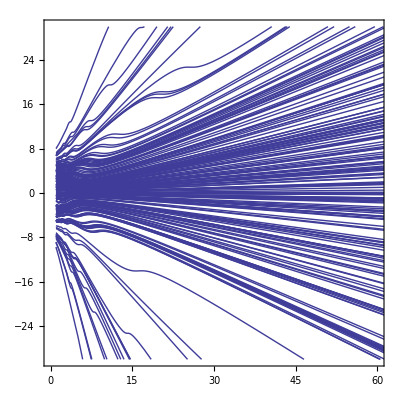

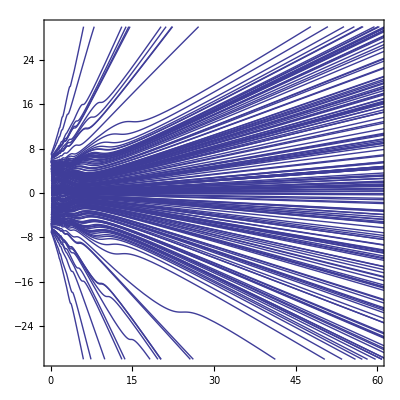

```mathematica
Plot[{(y[t])/.HollandtablU},{t,1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->30}]
```

-Graphics-

```mathematica
Plot[{(y[t])/.HollandtablU},{t,1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->26}]
```

-Graphics-

```mathematica
AAA =  1.0;
WIDTHVALUE =7;
ddd = 7.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 100;
swidth = 1;
phase = -π;
CHUNK = 4*16;
REPEAT = 100;
CUTTOFF = 80;

Close[outstream];
Close["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleSlitHist3.dat"];


Do[

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleSlitHist3.dat"];

ddd = 7.0;
www=1.0;
kkk = 1.0;

Parallelize[
HollandtablU=Table[NDSolve[{D[y[t], t]==VelocityField6[y[t], t, ddd ],y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,0.1,tmax}],{CHUNK}];
];


TestTableYU[t_] = Flatten[y[t]/.HollandtablU];


HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableYU[qqq]],NNN++,
For[ttt=0.1,ttt < tmax, ttt+=0.1, If[((TestTableYU[ttt][[NNN]])^2+(ttt)^2)>=CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[(TestTableYU[ttt][[NNN]])/(ttt)]];Break[]]]
];


Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]
,{REPEAT}];
```

General::openx: "/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleSlitHist3.dat" is not open.

$Aborted

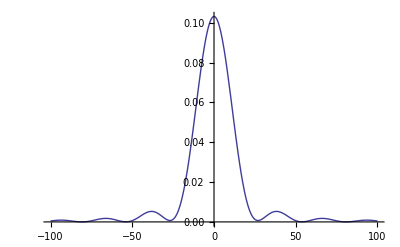

```mathematica
Plot[probdens[y,60,7],{y,-100,100},PlotRange->All]
```